```mathematica
D1//MatrixForm
```

(1/2 | -(√3)/2
-(√3)/2 | -1/2)

```mathematica
D1 = {{1, 0}, {0, 1}}
D2 = {{1/2, -Sqrt[3]/2}, {-Sqrt[3]/2, -1/2}}
D3 = {{-1/2, Sqrt[3]/2}, {-Sqrt[3]/2, -1/2}}
D4 = {{-1,0}, {0, 1}}
D5 = {{-1/2, -Sqrt[3]/2}, {Sqrt[3]/2, -1/2}}
D6 = {{1/2, Sqrt[3]/2}, {Sqrt[3]/2, -1/2}}
```

{{1,0},{0,1}}

{{1/2,-(√3)/2},{-(√3)/2,-1/2}}

{{-1/2,(√3)/2},{-(√3)/2,-1/2}}

{{-1,0},{0,1}}

{{-1/2,-(√3)/2},{(√3)/2,-1/2}}

{{1/2,(√3)/2},{(√3)/2,-1/2}}

```mathematica
T = {{t11, t12}, {t21, t22}
```

{{t11,t12},{t21,t22}}

```mathematica
H1 = D1 .T.D1†
H2 = D2 .T.D2†
H3 = D3 .T.D3†
H4 = D4 .T.D4†
H5 = D5 .T.D5†
H6 = D6 .T.D6†
```

{{t11,t12},{t21,t22}}

{{1/2 (t11/2-(√3 t21)/2)-1/2 √3 (t12/2-(√3 t22)/2),-1/2 √3 (t11/2-(√3 t21)/2)+1/2 (-t12/2+(√3 t22)/2)},{1/2 (-(√3 t11)/2-t21/2)-1/2 √3 (-(√3 t12)/2-t22/2),-1/2 √3 (-(√3 t11)/2-t21/2)+1/2 ((√3 t12)/2+t22/2)}}

{{1/2 (t11/2-(√3 t21)/2)+1/2 √3 (-t12/2+(√3 t22)/2),-1/2 √3 (-t11/2+(√3 t21)/2)+1/2 (t12/2-(√3 t22)/2)},{1/2 ((√3 t11)/2+t21/2)+1/2 √3 (-(√3 t12)/2-t22/2),-1/2 √3 (-(√3 t11)/2-t21/2)+1/2 ((√3 t12)/2+t22/2)}}

{{t11,-t12},{-t21,t22}}

{{1/2 (t11/2+(√3 t21)/2)-1/2 √3 (-t12/2-(√3 t22)/2),1/2 √3 (-t11/2-(√3 t21)/2)+1/2 (t12/2+(√3 t22)/2)},{1/2 (-(√3 t11)/2+t21/2)-1/2 √3 ((√3 t12)/2-t22/2),1/2 √3 ((√3 t11)/2-t21/2)+1/2 (-(√3 t12)/2+t22/2)}}

{{1/2 (t11/2+(√3 t21)/2)+1/2 √3 (t12/2+(√3 t22)/2),1/2 √3 (t11/2+(√3 t21)/2)+1/2 (-t12/2-(√3 t22)/2)},{1/2 ((√3 t11)/2-t21/2)+1/2 √3 ((√3 t12)/2-t22/2),1/2 √3 ((√3 t11)/2-t21/2)+1/2 (-(√3 t12)/2+t22/2)}}

```mathematica
H4[[1,1]]
```

t11

```mathematica
r1 = Cos[2a]+I*Sin[2a]
r2 = Cos[a-b]+I*Sin[a-b]
r3 = Cos[a+b]-I*Sin[a+b]
r4 = Cos[2a]-I*Sin[2a]
r5 = Cos[-a+b]+I*Sin[-a+b]
r6 = Cos[a+b]+I*Sin[a+b]
```

Cos[2 a]+i Sin[2 a]

Cos[a-b]+i Sin[a-b]

Cos[a+b]-i Sin[a+b]

Cos[2 a]-i Sin[2 a]

Cos[a-b]-i Sin[a-b]

Cos[a+b]+i Sin[a+b]

```mathematica
h11 = r1*H1[[1,1]]+r2*H2[[1,1]]+r3*H3[[1,1]]+r4*H4[[1,1]]+r5*H5[[1,1]]+r6*H6[[1,1]]
```

t11 (Cos[2 a]-i Sin[2 a])+t11 (Cos[2 a]+i Sin[2 a])+(1/2 (t11/2+(√3 t21)/2)-1/2 √3 (-t12/2-(√3 t22)/2)) (Cos[a-b]-i Sin[a-b])+(1/2 (t11/2-(√3 t21)/2)-1/2 √3 (t12/2-(√3 t22)/2)) (Cos[a-b]+i Sin[a-b])+(1/2 (t11/2-(√3 t21)/2)+1/2 √3 (-t12/2+(√3 t22)/2)) (Cos[a+b]-i Sin[a+b])+(1/2 (t11/2+(√3 t21)/2)+1/2 √3 (t12/2+(√3 t22)/2)) (Cos[a+b]+i Sin[a+b])

```mathematica
Simplify[h11]
```

2 t11 Cos[a]^2-2 t11 Sin[a]^2+Cos[a] ((t11+3 t22) Cos[b]+√3 i (t12+t21) Sin[b])

```mathematica
h22 = r1*H1[[2,2]]+r2*H2[[2,2]]+r3*H3[[2,2]]+r4*H4[[2,2]]+r5*H5[[2,2]]+r6*H6[[2,2]]
h12 = r1*H1[[1,2]]+r2*H2[[1,2]]+r3*H3[[1,2]]+r4*H4[[1,2]]+r5*H5[[1,2]]+r6*H6[[1,2]]
```

t22 (Cos[2 a]-i Sin[2 a])+t22 (Cos[2 a]+i Sin[2 a])+(1/2 √3 ((√3 t11)/2-t21/2)+1/2 (-(√3 t12)/2+t22/2)) (Cos[a-b]-i Sin[a-b])+(-1/2 √3 (-(√3 t11)/2-t21/2)+1/2 ((√3 t12)/2+t22/2)) (Cos[a-b]+i Sin[a-b])+(-1/2 √3 (-(√3 t11)/2-t21/2)+1/2 ((√3 t12)/2+t22/2)) (Cos[a+b]-i Sin[a+b])+(1/2 √3 ((√3 t11)/2-t21/2)+1/2 (-(√3 t12)/2+t22/2)) (Cos[a+b]+i Sin[a+b])

-t12 (Cos[2 a]-i Sin[2 a])+t12 (Cos[2 a]+i Sin[2 a])+(1/2 √3 (-t11/2-(√3 t21)/2)+1/2 (t12/2+(√3 t22)/2)) (Cos[a-b]-i Sin[a-b])+(-1/2 √3 (t11/2-(√3 t21)/2)+1/2 (-t12/2+(√3 t22)/2)) (Cos[a-b]+i Sin[a-b])+(-1/2 √3 (-t11/2+(√3 t21)/2)+1/2 (t12/2-(√3 t22)/2)) (Cos[a+b]-i Sin[a+b])+(1/2 √3 (t11/2+(√3 t21)/2)+1/2 (-t12/2-(√3 t22)/2)) (Cos[a+b]+i Sin[a+b])

```mathematica
Simplify[h12]
Simplify[h22]
```

Sin[a] (4 i t12 Cos[a]-i (t12-3 t21) Cos[b]+√3 (-t11+t22) Sin[b])

2 t22 Cos[a]^2-2 t22 Sin[a]^2+Cos[a] ((3 t11+t22) Cos[b]-√3 i (t12+t21) Sin[b])

```mathematica
h0=2*t0*(Cos[2a1]+2Cos[a1]*Cos[b1])+e1
h1=-2Sqrt[3]*t2*Sin[a1]*Sin[b1]+2*I*t1(Sin[2a1]+Sin[a1]*Cos[b1])
h2=2*t2*(Cos[2a1]-Cos[a1]*Cos[b1])+2Sqrt[3]*I*t1*Cos[a1]*Sin[b1]
h11=2*t11*Cos[2a1]+(t11+3*t22)*Cos[a1]*Cos[b1]+e2
h22=2*t22*Cos[2a1]+(t22+3*t11)*Cos[a1]*Cos[b1]+e2
h12=Sqrt[3]*(t22-t11)*Sin[a1]*Sin[b1]+4*I*t12*Sin[a1]*(Cos[a1]-Cos[b1])
```

1.046-0.368 (Cos[2 a1]+2 Cos[a1] Cos[b1])

(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]

1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]

2.104+0.436 Cos[2 a1]+0.389 Cos[a1] Cos[b1]

2.104+0.114 Cos[2 a1]+0.711 Cos[a1] Cos[b1]

(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]

```mathematica
HNN={{h0,h1,h2},
	{h1*,h11,h12},
	{h2*,h12*,h22}}
```

{{1.046-0.368 (Cos[2 a1]+2 Cos[a1] Cos[b1]),(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1],1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]},{Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]],2.104+0.436 Cos[2 a1]+0.389 Cos[a1] Cos[b1],(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]},{Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]],Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]],2.104+0.114 Cos[2 a1]+0.711 Cos[a1] Cos[b1]}}

```mathematica
Energy1=Eigenvalues[HNN,1]
Energy2=Eigenvalues[HNN,2]
Energy3=Eigenvalues[HNN,3]
```

{Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,1]}

{Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,1],Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,2]}

{Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,1],Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,2],Root[-4.63045+0.418637 Cos[2 a1]+2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1]+0.373859 Cos[2 a1]^2+0.442104 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]^2+0.0182911 Cos[2 a1]^3+0.837274 Cos[a1] Cos[b1]-2.13346 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]+1.014 Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]+1.33276 Cos[a1] Cos[2 a1] Cos[b1]-0.047658 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Cos[b1]+0.16698 Cos[a1] Cos[2 a1]^2 Cos[b1]+1.4141 Cos[a1]^2 Cos[b1]^2-0.394446 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1]^2+0.362577 Cos[a1]^2 Cos[2 a1] Cos[b1]^2+0.203562 Cos[a1]^3 Cos[b1]^3+(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[a1]+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+1.41419 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.497536 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Cos[b1] Sin[a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(0.+0.995072 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1]^2 Sin[a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1]^2-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1]^2 Sin[a1]^2+(0.+1.68741 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]+(0.+0.091428 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[2 a1]+(0.+0.570222 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[2 a1]+(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1] Sin[2 a1]-(1.0843+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1] Sin[2 a1]+(0.+2.92268 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]-(0.+1.3891 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[b1]+(0.+0.60565 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[2 a1] Sin[b1]+(0.+0.540362 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1]^2 Cos[b1] Sin[b1]-(3.69525+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.291688+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]-(0.200218+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]+(0.102621+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[2 a1] Sin[a1] Sin[b1]-(1.24873+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.205241+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Cos[b1] Sin[a1] Sin[b1]+(0.+2.37452 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[a1]^2 Sin[b1]-(0.+2.15087 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[b1] Sin[a1]^2 Sin[b1]+(0.+0.223646 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1] Sin[2 a1] Sin[b1]-(0.489762+0. ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Sin[a1]^2 Sin[b1]^2+(8.82838+0.183956 Cos[2 a1]-1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[2 a1]-0.152696 Cos[2 a1]^2+0.367912 Cos[a1] Cos[b1]+1.014 Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Cos[b1]-0.455258 Cos[a1] Cos[2 a1] Cos[b1]-0.533021 Cos[a1]^2 Cos[b1]^2-(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[a1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]+(0.+1.352 ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Cos[b1] Sin[a1]-(0.+0.802 ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[2 a1]-(0.+1.3891 ⅈ) Conjugate[1.014 (Cos[2 a1]-Cos[a1] Cos[b1])+(0.+1.3891 ⅈ) Cos[a1] Sin[b1]] Cos[a1] Sin[b1]+(1.7563+0. ⅈ) Conjugate[(0.+0.802 ⅈ) (Cos[b1] Sin[a1]+Sin[2 a1])-1.7563 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]+(0.27886+0. ⅈ) Conjugate[(0.+1.352 ⅈ) (Cos[a1]-Cos[b1]) Sin[a1]-0.27886 Sin[a1] Sin[b1]] Sin[a1] Sin[b1]) #1+(-5.254-0.182 Cos[2 a1]-0.364 Cos[a1] Cos[b1]) #1^2+#1^3&,3]}

```mathematica
ClearAll[a1,a2,b1,b2]
```

```mathematica
fx[x_]:=x
fy[y_]:=y
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

{2,5,10,17,26,37,50,65,82,101}

```mathematica
ky1=Array[#*0&,200]
```

```mathematica
ky2=Array[#*Pi/(100*Sqrt[3]*a)&,100,{0,99}]
```

```mathematica
ky3=Array[Pi/(Sqrt[3]*a)-#*(Pi)/(173*Sqrt[3]*a)&,174,{0,173}]
```

```mathematica
ky=Join[ky1,ky2,ky3]
```

3.19

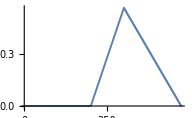

```mathematica
a=3.19
ListPlot[ky]
```

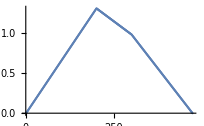

```mathematica
kx1=Array[#*4*Pi/(200*3*a)&,200,{0,199}]
kx2=Array[4*Pi/(3*a)-#*Pi/(100*3*a)&,100,{0,99}]
kx3=Array[Pi/a-#*(Pi)/(173*a)&,174,{0,173}]
kx=Join[kx1,kx2,kx3]
ListPlot[kx]
```

```mathematica
alpha=(1/2)*kx*a
beta=(Sqrt[3]/2)*ky*a
```

```mathematica
e1=1.046
e2=2.104
t0=-0.184
t1=0.401
t2=0.507
t11=0.218
t12=0.338
t22=0.057
```

```mathematica
band1=Array[#*0&,474]
band2=Array[#*0&,474]
band3=Array[#*0&,474]
For[i=1,i<=474,i++,
a1=alpha[[i]];
b1=beta[[i]];
band1[[i]]=Energy1;
band2[[i]]=Energy2;
band3[[i]]=Energy3;
]
```

```mathematica
x=Array[#&,474]
```

```mathematica
band3[[;;,1]]
```

{-0.058,-0.0580915,-0.0583657,-0.0588224,-0.0594611,-0.060281,-0.0612811,-0.0624604,-0.0638174,-0.0653506,-0.0670584,-0.0689387,-0.0709895,-0.0732085,-0.0755934,-0.0781414,-0.0808499,-0.0837161,-0.0867368,-0.0899091,-0.0932296,-0.096695,-0.100302,-0.104047,-0.107926,-0.111936,-0.116073,-0.120333,-0.124713,-0.129208,-0.133814,-0.138529,-0.143347,-0.148265,-0.153279,-0.158385,-0.163579,-0.168857,-0.174215,-0.17965,-0.185157,-0.190733,-0.196374,-0.202077,-0.207836,-0.21365,-0.219513,-0.225423,-0.231376,-0.237368,-0.243396,-0.249456,-0.255545,-0.261659,-0.267795,-0.27395,-0.28012,-0.286302,-0.292492,-0.298687,-0.304885,-0.311081,-0.317272,-0.323455,-0.329627,-0.335784,-0.341923,-0.348041,-0.354134,-0.360199,-0.366232,-0.372231,-0.378191,-0.384109,-0.389982,-0.395806,-0.401578,-0.407293,-0.412948,-0.41854,-0.424065,-0.429519,-0.434898,-0.440198,-0.445415,-0.450546,-0.455587,-0.460533,-0.46538,-0.470125,-0.474763,-0.47929,-0.483702,-0.487995,-0.492164,-0.496206,-0.500116,-0.50389,-0.507524,-0.511013,-0.514354,-0.517542,-0.520573,-0.523443,-0.526147,-0.528683,-0.531045,-0.53323,-0.535234,-0.537053,-0.538683,-0.54012,-0.541362,-0.542404,-0.543243,-0.543875,-0.544298,-0.544508,-0.544503,-0.544279,-0.543834,-0.543165,-0.54227,-0.541146,-0.539792,-0.538205,-0.536385,-0.534328,-0.532035,-0.529504,-0.526733,-0.523723,-0.520473,-0.516982,-0.513251,-0.50928,-0.505069,-0.50062,-0.495933,-0.49101,-0.485852,-0.480462,-0.474842,-0.468995,-0.462922,-0.456629,-0.450119,-0.443395,-0.436463,-0.429326,-0.421991,-0.414464,-0.406749,-0.398855,-0.390787,-0.382554,-0.374164,-0.365625,-0.356946,-0.348138,-0.339209,-0.330171,-0.321035,-0.311813,-0.302518,-0.293162,-0.283759,-0.274324,-0.264871,-0.255416,-0.245976,-0.236567,-0.227206,-0.217913,-0.208704,-0.1996,-0.190619,-0.181783,-0.173112,-0.164627,-0.156348,-0.148298,-0.140498,-0.13297,-0.125734,-0.118813,-0.112228,-0.105997,-0.100143,-0.0946823,-0.0896343,-0.0850156,-0.0808416,-0.0771267,-0.0738833,-0.0711223,-0.0688527,-0.0670815,-0.065814,-0.065053,-0.0647995,-0.0650523,-0.065808,-0.0670614,-0.0688052,-0.0710301,-0.0737253,-0.0768783,-0.0804748,-0.0844996,-0.0889361,-0.0937667,-0.0989729,-0.104536,-0.110435,-0.116651,-0.123164,-0.129953,-0.136997,-0.144277,-0.151771,-0.159461,-0.167327,-0.17535,-0.183511,-0.191792,-0.200177,-0.208647,-0.217187,-0.225781,-0.234415,-0.243073,-0.251743,-0.26041,-0.269064,-0.277692,-0.286283,-0.294826,-0.303311,-0.31173,-0.320073,-0.328332,-0.3365,-0.344569,-0.352532,-0.360383,-0.368117,-0.375728,-0.383212,-0.390563,-0.397778,-0.404853,-0.411785,-0.418571,-0.425208,-0.431694,-0.438027,-0.444206,-0.450228,-0.456093,-0.4618,-0.467348,-0.472737,-0.477967,-0.483037,-0.487948,-0.4927,-0.497293,-0.50173,-0.506009,-0.510132,-0.5141,-0.517915,-0.521577,-0.525088,-0.52845,-0.531663,-0.534729,-0.53765,-0.540427,-0.543061,-0.545556,-0.547911,-0.550129,-0.55221,-0.554157,-0.555971,-0.557654,-0.559206,-0.560628,-0.561923,-0.563091,-0.564134,-0.565051,-0.565844,-0.566515,-0.567062,-0.567487,-0.56779,-0.567972,-0.568033,-0.568028,-0.568011,-0.567983,-0.567944,-0.567894,-0.567832,-0.567757,-0.567671,-0.567571,-0.567458,-0.567332,-0.56719,-0.567034,-0.566862,-0.566674,-0.566468,-0.566244,-0.566001,-0.565738,-0.565454,-0.565148,-0.56482,-0.564467,-0.564089,-0.563685,-0.563253,-0.562792,-0.562302,-0.56178,-0.561225,-0.560637,-0.560013,-0.559353,-0.558655,-0.557917,-0.557138,-0.556317,-0.555453,-0.554543,-0.553587,-0.552583,-0.551529,-0.550424,-0.549267,-0.548057,-0.546791,-0.545468,-0.544088,-0.542649,-0.541148,-0.539586,-0.537961,-0.536271,-0.534515,-0.532693,-0.530802,-0.528842,-0.526812,-0.52471,-0.522535,-0.520287,-0.517965,-0.515568,-0.513094,-0.510543,-0.507915,-0.505209,-0.502424,-0.499559,-0.496614,-0.493589,-0.490483,-0.487296,-0.484027,-0.480677,-0.477246,-0.473733,-0.470138,-0.466463,-0.462705,-0.458867,-0.454949,-0.45095,-0.446872,-0.442715,-0.438479,-0.434166,-0.429776,-0.425311,-0.420771,-0.416158,-0.411472,-0.406715,-0.401889,-0.396994,-0.392033,-0.387008,-0.381919,-0.376769,-0.37156,-0.366293,-0.360972,-0.355598,-0.350173,-0.344701,-0.339183,-0.333622,-0.328021,-0.322382,-0.316709,-0.311005,-0.305272,-0.299514,-0.293734,-0.287935,-0.282121,-0.276296,-0.270462,-0.264624,-0.258785,-0.252949,-0.24712,-0.241303,-0.2355,-0.229716,-0.223956,-0.218223,-0.212521,-0.206856,-0.201231,-0.195651,-0.19012,-0.184643,-0.179224,-0.173867,-0.168578,-0.163361,-0.15822,-0.15316,-0.148185,-0.143301,-0.13851,-0.133819,-0.129231,-0.124751,-0.120383,-0.116131,-0.112,-0.107993,-0.104115,-0.10037,-0.0967621,-0.0932943,-0.0899705,-0.0867944,-0.0837693,-0.0808986,-0.0781852,-0.0756324,-0.0732428,-0.0710191,-0.0689639,-0.0670794,-0.0653678,-0.063831,-0.0624709,-0.0612889,-0.0602864,-0.0594645,-0.0588244,-0.0583666,-0.0580917,-0.058}

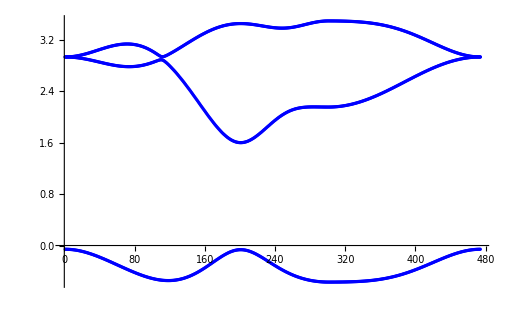

```mathematica
ListPlot[{band3[[;;,1]],band3[[;;,2]],band3[[;;,3]]},PlotStyle->{Blue,Blue,Blue}]
```

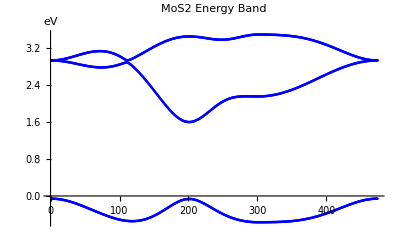

```mathematica
Show[%230,AxesLabel->{None,HoldForm[eV]},PlotLabel->HoldForm[MoS2 Energy Band],LabelStyle->{GrayLevel[0]}]
```

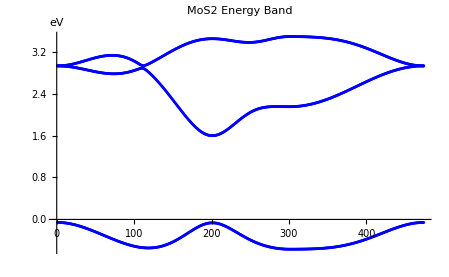

```mathematica
Show[%232,ImageSize->Full]
```

```mathematica
Show[%236,Ticks->{None,Automatic},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.72]],Method->{"OptimizePlotMarkers"->True,"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({Identity[#1⟦1⟧],Identity[#1⟦2⟧]}&),"CopiedValueFunction"->({Identity[#1⟦1⟧],Identity[#1⟦2⟧]}&)}}]
```

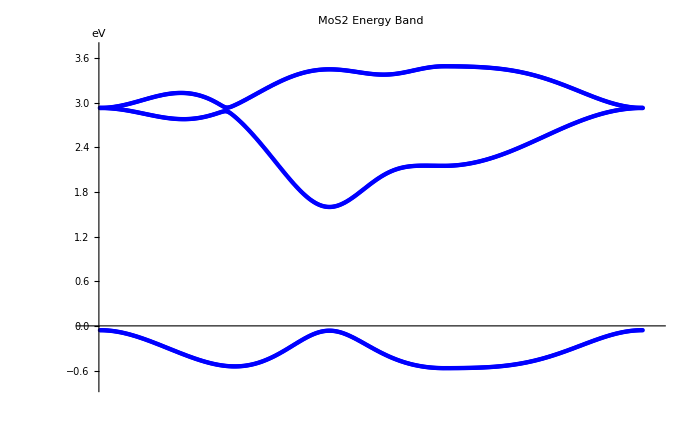

```mathematica
Export["/Users/xu/Desktop/MoS2.jpg",%228,"JPEG"]
```

/Users/xu/Desktop/MoS2.jpg